## IsoPerimetricRatio-example.nb

Example Cellzilla2D notebook.

GPL License applies. 
See http://xlr8r.info and http://cellzilla.info for further details.

```mathematica
<<Cellzilla2D.m;
```

Cellzilla2D (2.3.6 (10-Nov-2012)) loaded Sat 10 Nov 2012 09:39:50
using xCellerator 0.90 and XSSA 1204002
GPL License Terms Apply

```mathematica
polygon={{0.6656821861024209,0.5885139068629628},{0.3674265409089722,0.548792012192189},{-0.5083022778120968,0.03200749861905844},{-0.9625187848327785,-0.40634552703524995},{-0.603944818863048,-0.6296344493677282},{-0.2938861906733466,-0.19134629851828722},{0.3771323695082593,0.14124017268253336}};
```

```mathematica
IsoPerimetricRatio[polygon]
```

0.403407

```mathematica
4*Pi*Area[polygon]/Perimeter[polygon]^2
```

0.403407

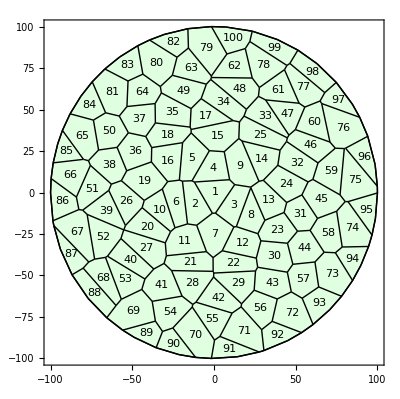

```mathematica
w=TemplateRandomCircularGrid[100,100];
ShowTissue[w,"CellNumbers"->True, Frame-> True]
```

```mathematica
IsoPerimetricRatio[w,1]
```

0.692296

```mathematica
IPR=IsoPerimetricRatio[w]
```

{0.692296,0.704169,0.709043,0.731707,0.728984,0.671409,0.839036,0.650823,0.768219,0.664026,0.80207,0.798919,0.779295,0.691025,0.756593,0.780512,0.65677,0.746387,0.842455,0.691244,0.657589,0.697932,0.850585,0.797323,0.675024,0.757814,0.685803,0.724273,0.70433,0.847464,0.860976,0.775481,0.598678,0.674952,0.780845,0.878714,0.857521,0.862399,0.649498,0.636723,0.83949,0.698714,0.83946,0.875572,0.82561,0.703013,0.663667,0.665868,0.785355,0.872723,0.724116,0.706112,0.641427,0.81034,0.681255,0.836514,0.87501,0.815829,0.715082,0.709305,0.705057,0.698829,0.751786,0.848638,0.808264,0.78528,0.680447,0.611832,0.828667,0.755825,0.759323,0.851691,0.855388,0.755874,0.675818,0.756892,0.68338,0.725746,0.785638,0.844125,0.847285,0.686593,0.723978,0.716388,0.614957,0.688601,0.488129,0.56001,0.661279,0.63025,0.545371,0.670252,0.741467,0.686181,0.600992,0.526985,0.603372,0.609498,0.601465,0.718025}

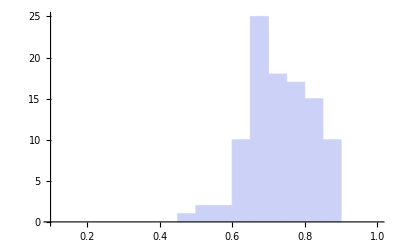

```mathematica
Histogram[IPR, {.1,1,.05}]
```